```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-EFTphysical-FA/Top-EFTphysical-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (EFT)

generic model {../../Models/Top-EFTphysical-FA/Top-EFTphysical-FA_FC} initialized

classes model {../../Models/Top-EFTphysical-FA/Top-EFTphysical-FA} initialized

in total: 2 Particles insertions

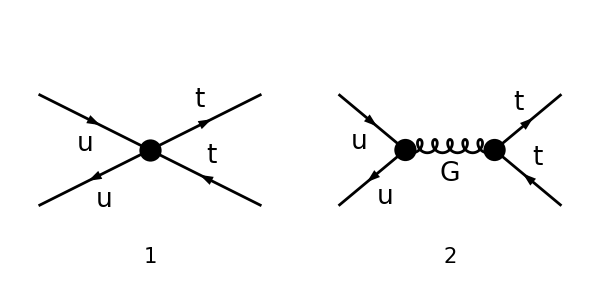

```mathematica
tops = CreateTopologies[0,2->2];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2]}, GenericModel->"../../Models/Top-EFTphysical-FA/Top-EFTphysical-FA_FC"];
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT,GaugeXi[a__]->1},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 2 Particles amplitudes

-1/6 ⅈ (alphaOqu8 (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^Ind25.(γ̄)^7.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT))+1/(p1+p2)^2 6 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (4 alphaOuG GS MT (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-2 alphaOuG GS ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+GS.GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+36 alphaOuu δ_Col1Col3 δ_Col2Col4 (φ(p1,MT)).γ^Ind24.(γ̄)^6.(φ(k1)) (φ(-k2)).γ^Ind24.(γ̄)^6.(φ(-p2,MT))+12 alphaOuu δ_Col1Col2 δ_Col3Col4 (φ(-k2)).γ^Ind26.(γ̄)^6.(φ(k1)) (φ(p1,MT)).γ^Ind26.(γ̄)^6.(φ(-p2,MT)))

```mathematica
fierzRules={Spinor[-Momentum[k2,D],0,1].DiracGamma[LorentzIndex[a_,D],D].DiracGamma[6].Spinor[-Momentum[p2,D],MT,1]*Spinor[Momentum[p1,D],MT,1].DiracGamma[LorentzIndex[a_,D],D].DiracGamma[6].Spinor[Momentum[k1,D],0,1]->-Spinor[-Momentum[k2,D],0,1].DiracGamma[LorentzIndex[a,D],D].DiracGamma[6].Spinor[Momentum[k1,D],0,1]*Spinor[Momentum[p1,D],MT,1].DiracGamma[LorentzIndex[a,D],D].DiracGamma[6].Spinor[-Momentum[p2,D],MT,1]};
```

```mathematica
ampC=ampB/.fierzRules
```

-1/6 ⅈ (alphaOqu8 (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^Ind25.(γ̄)^7.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT))+1/(p1+p2)^2 6 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (4 alphaOuG GS MT (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-2 alphaOuG GS ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+GS.GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))-36 alphaOuu δ_Col1Col3 δ_Col2Col4 (φ(-k2)).γ^Ind24.(γ̄)^6.(φ(k1)) (φ(p1,MT)).γ^Ind24.(γ̄)^6.(φ(-p2,MT))+12 alphaOuu δ_Col1Col2 δ_Col3Col4 (φ(-k2)).γ^Ind26.(γ̄)^6.(φ(k1)) (φ(p1,MT)).γ^Ind26.(γ̄)^6.(φ(-p2,MT)))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampC)/.{GS.GS-> GS^2},Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]]
```

-1/2 ⅈ alphaOqu8 δ_Col1Col3 δ_Col2Col4 (φ(-k2)).γ^Ind25.(γ̄)^7.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT))+1/6 ⅈ alphaOqu8 δ_Col1Col2 δ_Col3Col4 (φ(-k2)).γ^Ind25.(γ̄)^7.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT))-1/(p1+p2)^2 4 ⅈ alphaOuG GS MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-1/(p1+p2)^2 4 ⅈ alphaOuG GS MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT))+1/(p1+p2)^2 2 ⅈ alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))-1/(p1+p2)^2 2 ⅈ alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+1/(p1+p2)^2 2 ⅈ alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))-1/(p1+p2)^2 2 ⅈ alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))+6 ⅈ alphaOuu δ_Col1Col3 δ_Col2Col4 (φ(-k2)).γ^Ind24.(γ̄)^6.(φ(k1)) (φ(p1,MT)).γ^Ind24.(γ̄)^6.(φ(-p2,MT))-2 ⅈ alphaOuu δ_Col1Col2 δ_Col3Col4 (φ(-k2)).γ^Ind26.(γ̄)^6.(φ(k1)) (φ(p1,MT)).γ^Ind26.(γ̄)^6.(φ(-p2,MT))+-(ⅈ GS^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2

```mathematica
ampEsimp=FullSimplify[ampE/.{LorentzIndex[a_,D]->LorentzIndex[μ,D],alphaOqu8-> -12 alphaOuu}]
```

ⅈ (-(4 alphaOuG GS MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT))))/(p1+p2)^2-1/(p1+p2)^2 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))-2 alphaOuG ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))+2 alphaOuu (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) ((φ(-k2)).γ^μ.(γ̄)^6.(φ(k1))+(φ(-k2)).γ^μ.(γ̄)^7.(φ(k1))) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))

```mathematica
sps=Cases2[ampEsimp,Spinor]
moms=Cases2[ampEsimp2,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,(γ̄)^7,γ^μ,γ·p1,γ·p2}

```mathematica
(* Simpligy A.GA[6].(1,GA[mu]).B + A.GA[7].B - > A.(1,GA[mu]).B  *)
simp1=Flatten[Table[sps[[a]].moms[[1]].sps[[b]]+sps[[a]].moms[[2]].sps[[b]]-> sps[[a]].sps[[b]],{a,1,Length[sps]},{b,1,Length[sps]}]];
simp2=Flatten[Table[sps[[a]].moms[[3]].moms[[1]].sps[[b]]+sps[[a]].moms[[3]].moms[[2]].sps[[b]]-> sps[[a]].moms[[3]].sps[[b]],{a,1,Length[sps]},{b,1,Length[sps]}]];
```

```mathematica
ampEsimp2=FullSimplify[ampEsimp/.Join[simp1,simp2]]
```

ⅈ ((φ(-k2)).γ^μ.(φ(k1)) ((6 alphaOuu δ_Col1Col3 δ_Col2Col4-2 alphaOuu δ_Col1Col2 δ_Col3Col4) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(GS (4 alphaOuG MT+GS) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2)+(2 alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))/(p1+p2)^2)

```mathematica
Collect[ampEsimp2,{sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]],sps[[2]].moms[[5]].sps[[1]]},Simplify]
```

ⅈ (φ(-k2)).γ^μ.(φ(k1)) ((6 alphaOuu δ_Col1Col3 δ_Col2Col4-2 alphaOuu δ_Col1Col2 δ_Col3Col4) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(GS (4 alphaOuG MT+GS) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2)+(2 ⅈ alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/(p1+p2)^2-(2 ⅈ alphaOuG GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/(p1+p2)^2